NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 1 : Make a geometric plot to show that the n^th roots of unity are equally spaced points that lie on the unit circle C_1(0) = { z :|z| = 1} and form the vertices of a regular polygon with n sides, for n = 4, 5, 6, 7, 8.

n = 3

```mathematica
s=N[Solve[z^3==1,z]]
Subscript[z, 1]=s[[1,1,2]]
Subscript[z, 2]=s[[2,1,2]]
Subscript[z, 3]=s[[3,1,2]]
a=Graphics[{PointSize[0.03],Red,Point[{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}],Blue,Point[{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}],Yellow,Point[{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}]}];
b=PolarPlot[1,{h,0,2π},PolarAxes->True,PolarGridLines->True,PlotStyle->Thickness[0.01]];
c=Graphics[{Text[Style["z_1",Bold],{1.2,0.2}],Text[Style["z_2",Bold],{-0.8,-1}],Text[Style["z_3",Bold],{-0.8,1}]}];
e=Graphics[{Purple,Thick,Line[{{0,0},{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}}],Line[{{0,0},{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}}],Line[{{0,0},{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}}]}];
Show[a,b,c,e]
If[Arg[Subscript[z, 2]/Subscript[z, 1]]==Arg[Subscript[z, 3]/Subscript[z, 2]]==Arg[Subscript[z, 1]/Subscript[z, 3]],Print["All Points are equally spaced."],Print["All Points are not equally spaced."]]
f=Graphics[{Purple,Thick,Line[{{Re[Subscript[z, 1]],Im[Subscript[z, 1]]},{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}}],Line[{{Re[Subscript[z, 2]],Im[Subscript[z, 2]]},{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}}],Line[{{Re[Subscript[z, 3]],Im[Subscript[z, 3]]},{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}}]}];
Show[a,b,c,f]
If[Abs[Subscript[z, 1]-Subscript[z, 2]]==Abs[Subscript[z, 2]-Subscript[z, 3]]==Abs[Subscript[z, 3]-Subscript[z, 1]],Print["The Points form the vertices of a regular polygon."],Print["Polygon formed is not regular."]]
```

{{z→1.},{z→-0.5-0.866025 ⅈ},{z→-0.5+0.866025 ⅈ}}

1.

-0.5-0.866025 ⅈ

-0.5+0.866025 ⅈ

-Graphics-

All Points are equally spaced.

-Graphics-

The Points form the vertices of a regular polygon.

n = 4

```mathematica
s=N[Solve[z^4==1,z]]
Subscript[z, 1]=s[[1,1,2]]
Subscript[z, 2]=s[[2,1,2]]
Subscript[z, 3]=s[[3,1,2]]
Subscript[z, 4]=s[[4,1,2]]
a=Graphics[{PointSize[0.03],Red,Point[{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}],Blue,Point[{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}],Yellow,Point[{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}],Purple,Point[{Re[Subscript[z, 4]],Im[Subscript[z, 4]]}]}];
b=PolarPlot[1,{h,0,2π},PolarAxes->True,PolarGridLines->True,PlotStyle->Thickness[0.01]];
c=Graphics[{Text[Style["z_1",Bold],{-1.2,0}],Text[Style["z_2",Bold],{0,-1.2}],Text[Style["z_4",Bold],{1.2,0}],Text[Style["z_3",Bold],{0,1.2}]}];
e=Graphics[{Purple,Thick,Line[{{0,0},{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}}],Line[{{0,0},{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}}],Line[{{0,0},{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}}],Line[{{0,0},{Re[Subscript[z, 4]],Im[Subscript[z, 4]]}}]}];
Show[a,b,c,e]
If[Arg[Subscript[z, 3]/Subscript[z, 4]]==Arg[Subscript[z, 1]/Subscript[z, 3]]==Arg[Subscript[z, 2]/Subscript[z, 1]]==Arg[Subscript[z, 4]/Subscript[z, 2]],Print["All Points are equally spaced."],Print["All Points are not equally spaced."]]
f=Graphics[{Purple,Thick,Line[{{Re[Subscript[z, 4]],Im[Subscript[z, 4]]},{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}}],Line[{{Re[Subscript[z, 3]],Im[Subscript[z, 3]]},{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}}],Line[{{Re[Subscript[z, 1]],Im[Subscript[z, 1]]},{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}}],Line[{{Re[Subscript[z, 2]],Im[Subscript[z, 2]]},{Re[Subscript[z, 4]],Im[Subscript[z, 4]]}}]}];
Show[a,b,c,f]
If[Abs[Subscript[z, 4]-Subscript[z, 3]]==Abs[Subscript[z, 3]-Subscript[z, 1]]==Abs[Subscript[z, 1]-Subscript[z, 2]]==Abs[Subscript[z, 2]-Subscript[z, 4]],Print["The Points form the vertices of a regular polygon."],Print["Polygon formed is not regular."]]
```

{{z→-1.},{z→0.-1. ⅈ},{z→0.+1. ⅈ},{z→1.}}

-1.

0.-1. ⅈ

0.+1. ⅈ

1.

-Graphics-

All Points are equally spaced.

-Graphics-

The Points form the vertices of a regular polygon.

n = 5

```mathematica
s=N[Solve[z^5==1,z]]
Subscript[z, 1]=s[[1,1,2]]
Subscript[z, 2]=s[[2,1,2]]
Subscript[z, 3]=s[[3,1,2]]
Subscript[z, 4]=s[[4,1,2]]
Subscript[z, 5]=s[[5,1,2]]
a=Graphics[{PointSize[0.03],Red,Point[{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}],Blue,Point[{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}],Yellow,Point[{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}],Green,Point[{Re[Subscript[z, 4]],Im[Subscript[z, 4]]}],Magenta,Point[{Re[Subscript[z, 5]],Im[Subscript[z, 5]]}]}];
b=PolarPlot[1,{h,0,2π},PolarAxes->True,PolarGridLines->True,PlotStyle->Thickness[0.01]];
c=Graphics[{Text[Style["z_1",Bold],{1.2,0}],Text[Style["z_2",Bold],{-1,-0.6}],Text[Style["z_3",Bold],{0.5,1}],Text[Style["z_4",Bold],{0.5,-1}],Text[Style["z_5",Bold],{-1,0.6}]}];
e=Graphics[{Purple,Thick,Line[{{0,0},{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}}],Line[{{0,0},{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}}],Line[{{0,0},{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}}],Line[{{0,0},{Re[Subscript[z, 4]],Im[Subscript[z, 4]]}}],Line[{{0,0},{Re[Subscript[z, 5]],Im[Subscript[z, 5]]}}]}];
Show[a,b,c,e]
If[Arg[Subscript[z, 3]/Subscript[z, 1]]==Arg[Subscript[z, 5]/Subscript[z, 3]]==Arg[Subscript[z, 2]/Subscript[z, 5]]==Arg[Subscript[z, 4]/Subscript[z, 2]]==Arg[Subscript[z, 1]/Subscript[z, 4]],Print["All Points are equally spaced."],Print["All Points are not equally spaced."]]
f=Graphics[{Purple,Thick,Line[{{Re[Subscript[z, 1]],Im[Subscript[z, 1]]},{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}}],Line[{{Re[Subscript[z, 3]],Im[Subscript[z, 3]]},{Re[Subscript[z, 5]],Im[Subscript[z, 5]]}}],Line[{{Re[Subscript[z, 5]],Im[Subscript[z, 5]]},{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}}],Line[{{Re[Subscript[z, 2]],Im[Subscript[z, 2]]},{Re[Subscript[z, 4]],Im[Subscript[z, 4]]}}],Line[{{Re[Subscript[z, 4]],Im[Subscript[z, 4]]},{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}}]}];
Show[a,b,c,f]
If[Abs[Subscript[z, 1]-Subscript[z, 3]]==Abs[Subscript[z, 3]-Subscript[z, 5]]==Abs[Subscript[z, 5]-Subscript[z, 2]]==Abs[Subscript[z, 2]-Subscript[z, 4]]==Abs[Subscript[z, 4]-Subscript[z, 1]],Print["The Points form the vertices of a regular polygon."],Print["Polygon formed is not regular."]]
```

{{z→1.},{z→-0.809017-0.587785 ⅈ},{z→0.309017+0.951057 ⅈ},{z→0.309017-0.951057 ⅈ},{z→-0.809017+0.587785 ⅈ}}

1.

-0.809017-0.587785 ⅈ

0.309017+0.951057 ⅈ

0.309017-0.951057 ⅈ

-0.809017+0.587785 ⅈ

-Graphics-

All Points are equally spaced.

-Graphics-

The Points form the vertices of a regular polygon.

n = 6

```mathematica
s=N[Solve[z^6==1,z]]
Subscript[z, 1]=s[[1,1,2]]
Subscript[z, 2]=s[[2,1,2]]
Subscript[z, 3]=s[[3,1,2]]
Subscript[z, 4]=s[[4,1,2]]
Subscript[z, 5]=s[[5,1,2]]
Subscript[z, 6]=s[[6,1,2]]
a=Graphics[{PointSize[0.03],Red,Point[{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}],Blue,Point[{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}],Yellow,Point[{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}],Green,Point[{Re[Subscript[z, 4]],Im[Subscript[z, 4]]}],Magenta,Point[{Re[Subscript[z, 5]],Im[Subscript[z, 5]]}],Purple,Point[{Re[Subscript[z, 6]],Im[Subscript[z, 6]]}]}];
b=PolarPlot[1,{h,0,2π},PolarAxes->True,PolarGridLines->True,PlotStyle->Thickness[0.01]];
c=Graphics[{Text[Style["z_1",Bold],{-1.2,0.2}],Text[Style["z_2",Bold],{1.2,0.2}],Text[Style["z_3",Bold],{-0.8,-1}],Text[Style["z_4",Bold],{0.8,1}],Text[Style["z_5",Bold],{0.8,-1}],Text[Style["z_6",Bold],{-0.8,1}]}];
e=Graphics[{Purple,Thick,Line[{{0,0},{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}}],Line[{{0,0},{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}}],Line[{{0,0},{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}}],Line[{{0,0},{Re[Subscript[z, 4]],Im[Subscript[z, 4]]}}],Line[{{0,0},{Re[Subscript[z, 5]],Im[Subscript[z, 5]]}}],Line[{{0,0},{Re[Subscript[z, 6]],Im[Subscript[z, 6]]}}]}];
Show[a,b,c,e]
If[Arg[Subscript[z, 4]/Subscript[z, 2]]==Arg[Subscript[z, 6]/Subscript[z, 4]]==Arg[Subscript[z, 1]/Subscript[z, 6]]==Arg[Subscript[z, 3]/Subscript[z, 1]]==Arg[Subscript[z, 5]/Subscript[z, 3]]==Arg[Subscript[z, 2]/Subscript[z, 5]],Print["All Points are equally spaced."],Print["All Points are not equally spaced."]]
f=Graphics[{Purple,Thick,Line[{{Re[Subscript[z, 2]],Im[Subscript[z, 2]]},{Re[Subscript[z, 4]],Im[Subscript[z, 4]]}}],Line[{{Re[Subscript[z, 4]],Im[Subscript[z, 4]]},{Re[Subscript[z, 6]],Im[Subscript[z, 6]]}}],Line[{{Re[Subscript[z, 6]],Im[Subscript[z, 6]]},{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}}],Line[{{Re[Subscript[z, 1]],Im[Subscript[z, 1]]},{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}}],Line[{{Re[Subscript[z, 3]],Im[Subscript[z, 3]]},{Re[Subscript[z, 5]],Im[Subscript[z, 5]]}}],Line[{{Re[Subscript[z, 5]],Im[Subscript[z, 5]]},{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}}]}];
Show[a,b,c,f]
If[Abs[Subscript[z, 2]-Subscript[z, 4]]==Abs[Subscript[z, 4]-Subscript[z, 6]]==Abs[Subscript[z, 6]-Subscript[z, 1]]==Abs[Subscript[z, 1]-Subscript[z, 3]]==Abs[Subscript[z, 3]-Subscript[z, 5]]==Abs[Subscript[z, 5]-Subscript[z, 2]],Print["The Points form the vertices of a regular polygon."],Print["Polygon formed is not regular."]]
```

{{z→-1.},{z→1.},{z→-0.5-0.866025 ⅈ},{z→0.5+0.866025 ⅈ},{z→0.5-0.866025 ⅈ},{z→-0.5+0.866025 ⅈ}}

-1.

1.

-0.5-0.866025 ⅈ

0.5+0.866025 ⅈ

0.5-0.866025 ⅈ

-0.5+0.866025 ⅈ

-Graphics-

All Points are equally spaced.

-Graphics-

The Points form the vertices of a regular polygon.

n = 7

```mathematica
s=N[Solve[z^7==1,z]]
Subscript[z, 1]=s[[1,1,2]]
Subscript[z, 2]=s[[2,1,2]]
Subscript[z, 3]=s[[3,1,2]]
Subscript[z, 4]=s[[4,1,2]]
Subscript[z, 5]=s[[5,1,2]]
Subscript[z, 6]=s[[6,1,2]]
Subscript[z, 7]=s[[7,1,2]]
a=Graphics[{PointSize[0.03],Red,Point[{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}],Blue,Point[{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}],Yellow,Point[{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}],Green,Point[{Re[Subscript[z, 4]],Im[Subscript[z, 4]]}],Magenta,Point[{Re[Subscript[z, 5]],Im[Subscript[z, 5]]}],Purple,Point[{Re[Subscript[z, 6]],Im[Subscript[z, 6]]}],Brown,Point[{Re[Subscript[z, 7]],Im[Subscript[z, 7]]}]}];
b=PolarPlot[1,{h,0,2π},PolarAxes->True,PolarGridLines->True,PlotStyle->Thickness[0.01]];
c=Graphics[{Text[Style["z_1",Bold],{1.2,0}],Text[Style["z_2",Bold],{-1.2,-0.6}],Text[Style["z_3",Bold],{0.9,1}],Text[Style["z_4",Bold],{-0.4,-1.2}],Text[Style["z_5",Bold],{-0.4,1.2}],Text[Style["z_6",Bold],{0.9,-1}],Text[Style["z_7",Bold],{-1.2,0.6}]}];
e=Graphics[{Purple,Thick,Line[{{0,0},{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}}],Line[{{0,0},{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}}],Line[{{0,0},{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}}],Line[{{0,0},{Re[Subscript[z, 4]],Im[Subscript[z, 4]]}}],Line[{{0,0},{Re[Subscript[z, 5]],Im[Subscript[z, 5]]}}],Line[{{0,0},{Re[Subscript[z, 6]],Im[Subscript[z, 6]]}}],Line[{{0,0},{Re[Subscript[z, 7]],Im[Subscript[z, 7]]}}]}];
Show[a,b,c,e]
If[Arg[Subscript[z, 3]/Subscript[z, 1]]==Arg[Subscript[z, 5]/Subscript[z, 3]]==Arg[Subscript[z, 7]/Subscript[z, 5]]==Arg[Subscript[z, 2]/Subscript[z, 7]]==Arg[Subscript[z, 4]/Subscript[z, 2]]==Arg[Subscript[z, 6]/Subscript[z, 4]]==Arg[Subscript[z, 1]/Subscript[z, 6]],Print["All Points are equally spaced."],Print["All Points are not equally spaced."]]
f=Graphics[{Purple,Thick,Line[{{Re[Subscript[z, 1]],Im[Subscript[z, 1]]},{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}}],Line[{{Re[Subscript[z, 3]],Im[Subscript[z, 3]]},{Re[Subscript[z, 5]],Im[Subscript[z, 5]]}}],Line[{{Re[Subscript[z, 5]],Im[Subscript[z, 5]]},{Re[Subscript[z, 7]],Im[Subscript[z, 7]]}}],Line[{{Re[Subscript[z, 7]],Im[Subscript[z, 7]]},{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}}],Line[{{Re[Subscript[z, 2]],Im[Subscript[z, 2]]},{Re[Subscript[z, 4]],Im[Subscript[z, 4]]}}],Line[{{Re[Subscript[z, 4]],Im[Subscript[z, 4]]},{Re[Subscript[z, 6]],Im[Subscript[z, 6]]}}],Line[{{Re[Subscript[z, 6]],Im[Subscript[z, 6]]},{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}}]}];
Show[a,b,c,f]
If[Abs[Subscript[z, 1]-Subscript[z, 3]]==Abs[Subscript[z, 3]-Subscript[z, 5]]==Abs[Subscript[z, 5]-Subscript[z, 7]]==Abs[Subscript[z, 7]-Subscript[z, 2]]==Abs[Subscript[z, 2]-Subscript[z, 4]]==Abs[Subscript[z, 4]-Subscript[z, 6]]==Abs[Subscript[z, 6]-Subscript[z, 1]],Print["The Points form the vertices of a regular polygon."],Print["Polygon formed is not regular."]]
```

{{z→1.},{z→-0.900969-0.433884 ⅈ},{z→0.62349+0.781831 ⅈ},{z→-0.222521-0.974928 ⅈ},{z→-0.222521+0.974928 ⅈ},{z→0.62349-0.781831 ⅈ},{z→-0.900969+0.433884 ⅈ}}

1.

-0.900969-0.433884 ⅈ

0.62349+0.781831 ⅈ

-0.222521-0.974928 ⅈ

-0.222521+0.974928 ⅈ

0.62349-0.781831 ⅈ

-0.900969+0.433884 ⅈ

-Graphics-

All Points are not equally spaced.

-Graphics-

The Points form the vertices of a regular polygon.

n = 8

```mathematica
s=N[Solve[z^8==1,z]]
Subscript[z, 1]=s[[1,1,2]]
Subscript[z, 2]=s[[2,1,2]]
Subscript[z, 3]=s[[3,1,2]]
Subscript[z, 4]=s[[4,1,2]]
Subscript[z, 5]=s[[5,1,2]]
Subscript[z, 6]=s[[6,1,2]]
Subscript[z, 7]=s[[7,1,2]]
Subscript[z, 8]=s[[8,1,2]]
a=Graphics[{PointSize[0.03],Red,Point[{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}],Blue,Point[{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}],Yellow,Point[{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}],Green,Point[{Re[Subscript[z, 4]],Im[Subscript[z, 4]]}],Magenta,Point[{Re[Subscript[z, 5]],Im[Subscript[z, 5]]}],Purple,Point[{Re[Subscript[z, 6]],Im[Subscript[z, 6]]}],Brown,Point[{Re[Subscript[z, 7]],Im[Subscript[z, 7]]}],Orange,Point[{Re[Subscript[z, 8]],Im[Subscript[z, 8]]}]}];
b=PolarPlot[1,{h,0,2π},PolarAxes->True,PolarGridLines->True,PlotStyle->Thickness[0.01]];
c=Graphics[{Text[Style["z_1",Bold],{-1.2,0}],Text[Style["z_2",Bold],{0,-1.2}],Text[Style["z_3",Bold],{0,1.2}],Text[Style["z_4",Bold],{1.2,0}],Text[Style["z_5",Bold],{-1,-1}],Text[Style["z_6",Bold],{1,1}],Text[Style["z_7",Bold],{1,-1}],Text[Style["z_8",Bold],{-1,1}]}];
e=Graphics[{Purple,Thick,Line[{{0,0},{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}}],Line[{{0,0},{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}}],Line[{{0,0},{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}}],Line[{{0,0},{Re[Subscript[z, 4]],Im[Subscript[z, 4]]}}],Line[{{0,0},{Re[Subscript[z, 5]],Im[Subscript[z, 5]]}}],Line[{{0,0},{Re[Subscript[z, 6]],Im[Subscript[z, 6]]}}],Line[{{0,0},{Re[Subscript[z, 7]],Im[Subscript[z, 7]]}}],Line[{{0,0},{Re[Subscript[z, 8]],Im[Subscript[z, 8]]}}]}];
Show[a,b,c,e]
If[Arg[Subscript[z, 3]/Subscript[z, 6]]==Arg[Subscript[z, 8]/Subscript[z, 3]]==Arg[Subscript[z, 1]/Subscript[z, 8]]==Arg[Subscript[z, 5]/Subscript[z, 1]]==Arg[Subscript[z, 2]/Subscript[z, 5]]==Arg[Subscript[z, 7]/Subscript[z, 2]]==Arg[Subscript[z, 4]/Subscript[z, 7]]==Arg[Subscript[z, 6]/Subscript[z, 4]]==Arg[Subscript[z, 3]/Subscript[z, 6]],Print["All Points are equally spaced."],Print["All Points are not equally spaced."]]
f=Graphics[{Purple,Thick,Line[{{Re[Subscript[z, 6]],Im[Subscript[z, 6]]},{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}}],Line[{{Re[Subscript[z, 3]],Im[Subscript[z, 3]]},{Re[Subscript[z, 8]],Im[Subscript[z, 8]]}}],Line[{{Re[Subscript[z, 8]],Im[Subscript[z, 8]]},{Re[Subscript[z, 1]],Im[Subscript[z, 1]]}}],Line[{{Re[Subscript[z, 1]],Im[Subscript[z, 1]]},{Re[Subscript[z, 5]],Im[Subscript[z, 5]]}}],Line[{{Re[Subscript[z, 5]],Im[Subscript[z, 5]]},{Re[Subscript[z, 2]],Im[Subscript[z, 2]]}}],Line[{{Re[Subscript[z, 2]],Im[Subscript[z, 2]]},{Re[Subscript[z, 7]],Im[Subscript[z, 7]]}}],Line[{{Re[Subscript[z, 7]],Im[Subscript[z, 7]]},{Re[Subscript[z, 4]],Im[Subscript[z, 4]]}}],Line[{{Re[Subscript[z, 4]],Im[Subscript[z, 4]]},{Re[Subscript[z, 6]],Im[Subscript[z, 6]]}}],Line[{{Re[Subscript[z, 6]],Im[Subscript[z, 6]]},{Re[Subscript[z, 3]],Im[Subscript[z, 3]]}}]}];
Show[a,b,c,f]
If[Abs[Subscript[z, 6]-Subscript[z, 3]]==Abs[Subscript[z, 3]-Subscript[z, 8]]==Abs[Subscript[z, 8]-Subscript[z, 1]]==Abs[Subscript[z, 1]-Subscript[z, 5]]==Abs[Subscript[z, 5]-Subscript[z, 2]]==Abs[Subscript[z, 2]-Subscript[z, 7]]==Abs[Subscript[z, 7]-Subscript[z, 4]]==Abs[Subscript[z, 4]-Subscript[z, 6]]==Abs[Subscript[z, 6]-Subscript[z, 3]],Print["The Points form the vertices of a regular polygon."],Print["Polygon formed is not regular."]]
```

{{z→-1.},{z→0.-1. ⅈ},{z→0.+1. ⅈ},{z→1.},{z→-0.707107-0.707107 ⅈ},{z→0.707107+0.707107 ⅈ},{z→0.707107-0.707107 ⅈ},{z→-0.707107+0.707107 ⅈ}}

-1.

0.-1. ⅈ

0.+1. ⅈ

1.

-0.707107-0.707107 ⅈ

0.707107+0.707107 ⅈ

0.707107-0.707107 ⅈ

-0.707107+0.707107 ⅈ

-Graphics-

All Points are equally spaced.

-Graphics-

The Points form the vertices of a regular polygon.

NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 2 : Find all the solutions of the equation z^3=8i and represent these geometrically.

(a) Solve the equation z^3 = 8i

```mathematica
sol=N[Solve[z^3==8I,z]]
```

{{z→0.-2. ⅈ},{z→1.73205+1. ⅈ},{z→-1.73205+1. ⅈ}}

```mathematica
z1=sol[[1,1,2]]
z2=sol[[2,1,2]]
z3=sol[[3,1,2]]
```

0.-2. ⅈ

1.73205+1. ⅈ

-1.73205+1. ⅈ

(b) Show that the roots lie on a circle with radius 2, centered at origin

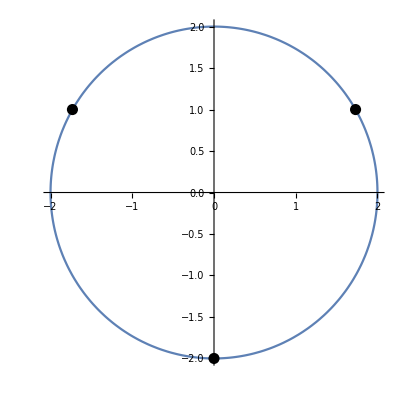

```mathematica
a=Graphics[{PointSize[0.02],
Point[{Re[z1],Im[z1]}],
Point[{Re[z2],Im[z2]}],
Point[{Re[z3],Im[z3]}]
}];
b=PolarPlot[2,{τ,0,2π}];
Show[b,a]
```

NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 3 : Write the parametric equations and make a parametric plot for an ellipse centered at the origin with the horizontal major axis of 4 units and vertical minor axis of 2 units

(a) Write parametric equations and make a parametric plot for an ellipse centered at the origin with horizontal major axis of 4 units and vertical minor axis of 2 units. 
(b) Show the effect of rotation of this ellipse by an angle of π/6 radians and shifting of the centre from (0,0) to (2,1), by making a parametric plot.

```mathematica
(*To plot a parametric equations, we may use the ParametricPlot[] command*)
```

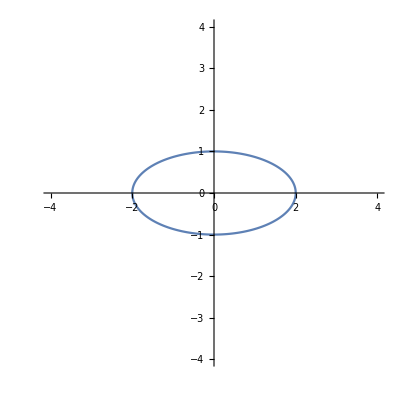

```mathematica
(*the equation of the ellipse is x^2/2^2+y^2/1=1*)
a=ParametricPlot[{2*Cos[t], Sin[t]},{t,0,2π},PlotRange->4]
```

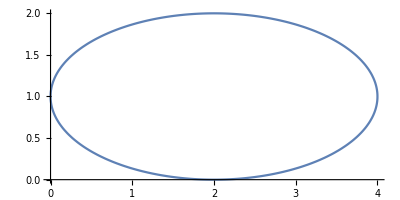

```mathematica
(*Translate the center to the point (2,1)*)
b=ParametricPlot[{2*Cos[t]+2, Sin[t]+1},{t,0,2π}]
```

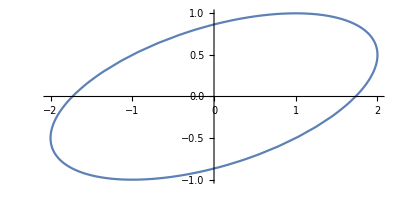

```mathematica
(*Rotate the ellipse about the origin by an angle of π/6*)
c=ParametricPlot[{2*Cos[t], Sin[t+π/6]},{t,0,2π}]
```

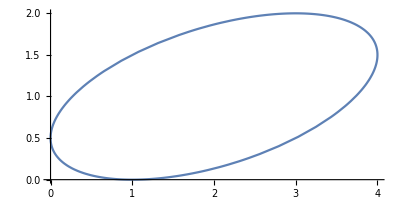

```mathematica
(*Rotate and translate*)
d=ParametricPlot[{2*Cos[t]+2, Sin[t+π/6]+1},{t,0,2π}]
```

Using ParametricPlot command

```mathematica
ClearAll;
```

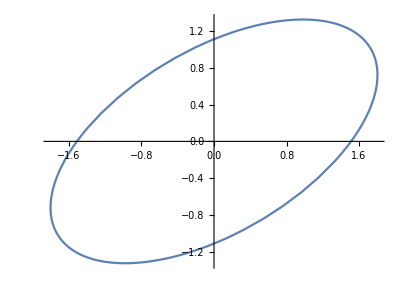

```mathematica
e=ParametricPlot[RotationTransform[π/6][{2*Cos[t], Sin[t]}],{t,0,2π}]
```

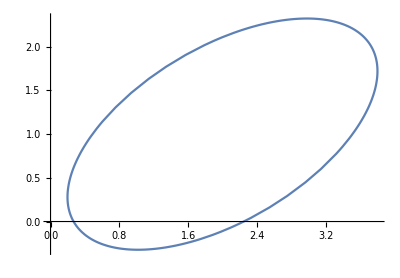

```mathematica
f=ParametricPlot[TranslationTransform[{2,1}][RotationTransform[π/6][{2*Cos[t], Sin[t]}]],{t,0,2π}]
```

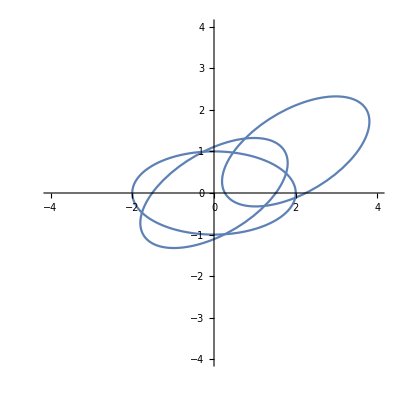

```mathematica
Show[a,e,f]
```

```mathematica
ClearAll;
a=ParametricPlot[
{{2Cos[t], Sin[t]},
RotationTransform[π/6][{2Cos[t], Sin[t]}],
TranslationTransform[{2,1}][RotationTransform[π/6][{2Cos[t], Sin[t]}]]},
{t,0,2π},PlotLegends->{"Ellipse", "Rotated Ellipse", "Rotated and Translated Ellipse"},AxesLabel->{"Real Axis","Imaginary Axis"},PlotRange->4
];
b=PolarPlot[2,{θ,0,2π},PolarGridLines->True,PlotStyle->Opacity[0],PolarAxes->True];
Show[a,b]
```

-Graphics-

```mathematica
Manipulate[
ParametricPlot[
{{2Cos[t], Sin[t]},
RotationTransform[π/6][{2Cos[t], Sin[t]}],
TranslationTransform[{2,1}][RotationTransform[τ][{2Cos[t], Sin[t]}]]},
{t,0,2π},PlotLegends->{"Ellipse", "Rotated Ellipse", "Rotated and Translated Ellipse"}
],{τ,0,2π}
]
```

NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 4 : Show that the image of the open disk D_1(-1,-i)= {z : |z+1+i|<1} under the linear transformation w = f(z) = (3-4i) z + 6 + 2i is the open disk:
D_5(-1+3i) = {w: |w+1-3i|<5}.

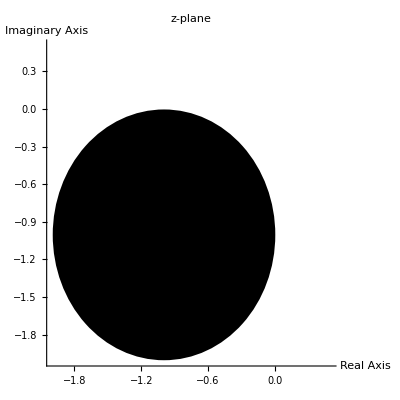

```mathematica
a=Region[Disk[{-1,-1},1],Axes->True,AxesLabel->{"Real Axis", "Imaginary Axis"},PlotLabel->"z-plane",PlotRange->{{-2,0.5},{-2,0.5}}]
```

```mathematica
z=x+ⅈy
```

x+ⅈy

```mathematica
w=ComplexExpand[(3-4ⅈ)z+(6+2ⅈ)]
```

6+3 x+ⅈ (2-4 x-4 ⅈy)+3 ⅈy

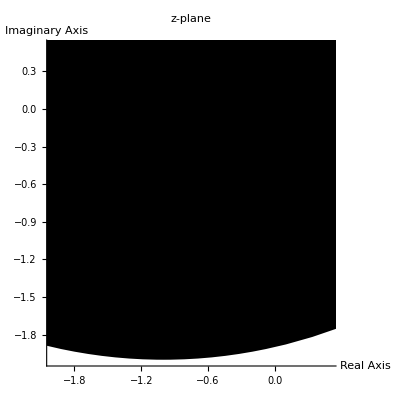

```mathematica
b=Region[
TransformedRegion[a,Function[p,{6+3p[[1]]+4p[[2]],2-4p[[1]]+3p[[2]]}]],
PlotLabel->"w-plane",PlotRange->{{-7,5},{-3,9}}
]
```

```mathematica
RegionCentroid[b]
```

{-1.,3.}

```mathematica
radius=√(Area[b]/π)
```

5.

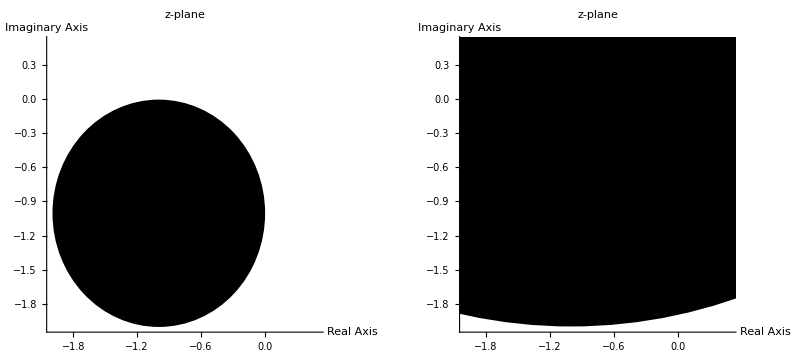

```mathematica
GraphicsRow[{a,b}]
```

NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 5 : Show that the image of the half plane Re[z]>1 under the linear  transformation ω=f(z)=(-1+i)z+(-2+3i) is the half plane {w:v>u+7} where u=Re[ω] and v=Im[ω].

```mathematica
a=Region[
HalfPlane[{{1,-5},{1,9}},{1,0}],Axes->True,PlotRange->{{-20,20},{-20,20}},
AxesLabel->{"Real Axis","Imaginary Axis"},
PlotLabel->"Image in z-plane"
]
```

-Graphics-

```mathematica
Area[a]
```

∞

```mathematica
z=x+y*ⅈ
```

x+ⅈ y

```mathematica
ω=ComplexExpand[(-1+ⅈ)*z+(-2+3ⅈ)]
```

-2-x+ⅈ (3+x-y)-y

```mathematica
b=Region[
TransformedRegion[a,Function[p,{-2-p[[1]]-p[[2]],3+p[[1]]-p[[2]]}]],
Axes->True,PlotRange->{{-20,20},{-20,20}},
AxesLabel->{"Real Axis","Imaginary Axis"},
PlotLabel->"Image in ω-plane"
]
```

-Graphics-

```mathematica
Area[b]
```

∞

```mathematica
GraphicsRow[{a,b},Frame->All]
```

-Graphics-

NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 6 : Show that image of the half plane {z: Re[z] >= 1/2 } under the linear transformation ω=f(z)=1/2 is the disk {ω: |ω - 1| < 1}

```mathematica
z=x+ⅈ*y
```

x+ⅈ y

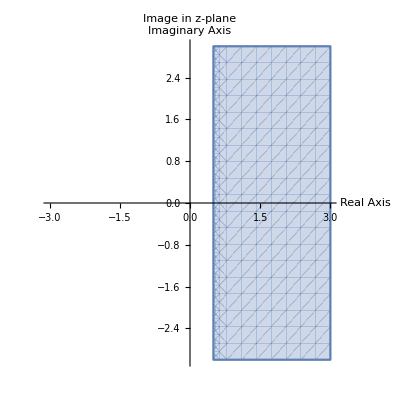

```mathematica
a=RegionPlot[
Re[z]>=1/2,{x,-3,3},{y,-3,3},Axes->True,Frame->False,
AxesLabel->{"Real Axis","Imaginary Axis"},PlotLabel->"Image in z-plane"
]
```

```mathematica
f[z_]:=1/z
```

```mathematica
ω=ComplexExpand[f[z]]
```

x/(x^2+y^2)-(ⅈ y)/(x^2+y^2)

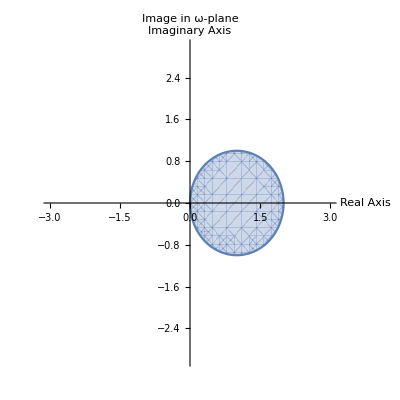

```mathematica
b=RegionPlot[
Re[1/z]>=1/2,{x,-3,3},{y,-3,3},Axes->True,Frame->False,
AxesLabel->{"Real Axis","Imaginary Axis"},PlotLabel->"Image in ω-plane"
]
```

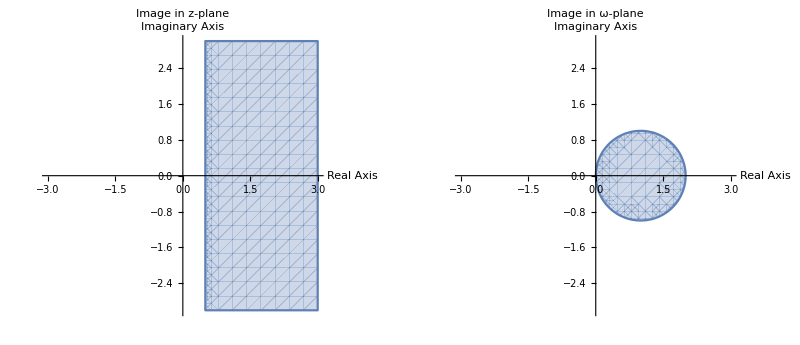

```mathematica
GraphicsRow[{a,b},Frame->All]
```

NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 7 : Plot the lines y = a, where a = -1/2, -1, 1/2, 1; the lines x = a where a = -1/2, -1, 1/2, 1; and the corresponding grid. Also find the image of this grid under the mapping f(z) = 1/z .

```mathematica
f[z_] := 1 / z
```

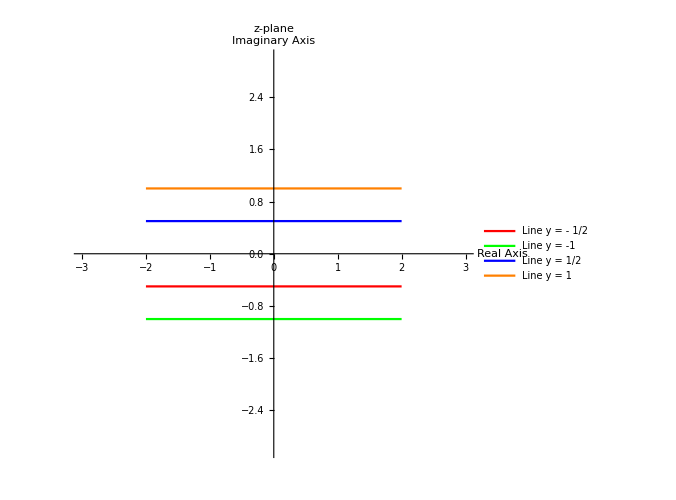

```mathematica
a1 = ParametricPlot[Evaluate[Table[{Re[t + ⅈ a], Im[t + ⅈ a]}, {a, {- 1/2 , -1, 1/2 , 1}}]], {t, -2, 2}, PlotStyle -> {Red, Green, Blue, Orange}, Axes -> True, Frame -> False, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotLabel -> "z-plane", PlotLegends -> {"Line y = - 1/2 ", "Line y = -1", "Line y = 1/2 ", "Line y = 1"}, PlotRange -> 3, ImageSize -> {500, 500}]
```

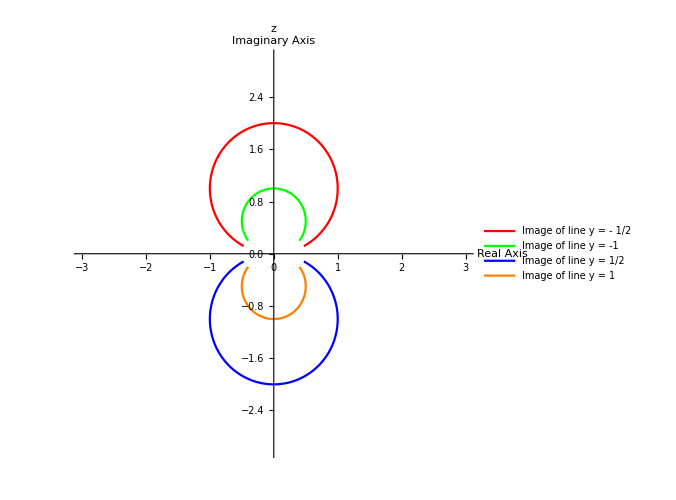

```mathematica
b1 = ParametricPlot[ Evaluate[Table[{Re[f[t + ⅈ a]], Im[f[t + ⅈ a]]}, {a, {- 1/2 , -1, 1/2 , 1}}]], {t, -2, 2}, PlotStyle -> {Red, Green, Blue, Orange}, Axes -> True, Frame -> False, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotLabel -> "z", PlotLegends -> {"Image of line y = - 1/2 ", "Image of line y = -1", "Image of line y = 1/2 ", "Image of line y = 1"}, PlotRange -> 3, ImageSize -> {500, 500}]
```

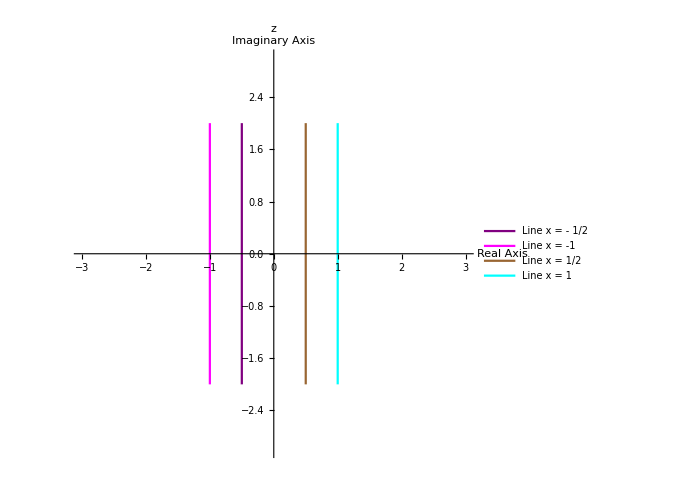

```mathematica
a2 = ParametricPlot[Evaluate[Table[{Re[a + ⅈ t], Im[a +ⅈ t]}, {a, {- 1/2 , -1, 1/2 , 1}}]], {t, -2, 2}, PlotStyle -> {Purple, Magenta, Brown, Cyan}, Axes -> True, Frame -> False, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotLabel -> "z", PlotLegends -> {"Line x = - 1/2 ", "Line x = -1", "Line x = 1/2 ", "Line x = 1"}, PlotRange -> 3, ImageSize -> {500, 500}]
```

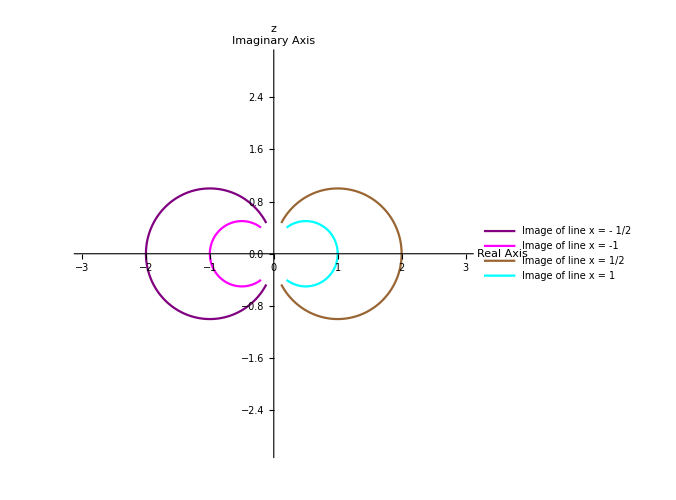

```mathematica
b2 = ParametricPlot[ Evaluate[Table[{Re[f[a + ⅈ t]], Im[f[a + ⅈ t]]}, {a, {- 1/2 , -1, 1/2 , 1}}]], {t, -2, 2}, PlotStyle -> {Purple, Magenta, Brown, Cyan}, Axes -> True, Frame -> False, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotLabel -> "z", PlotLegends -> {"Image of line x = - 1/2 ", "Image of line x = -1", "Image of line x = 1/2 ", "Image of line x = 1"}, PlotRange -> 3, ImageSize -> {500, 500}]
```

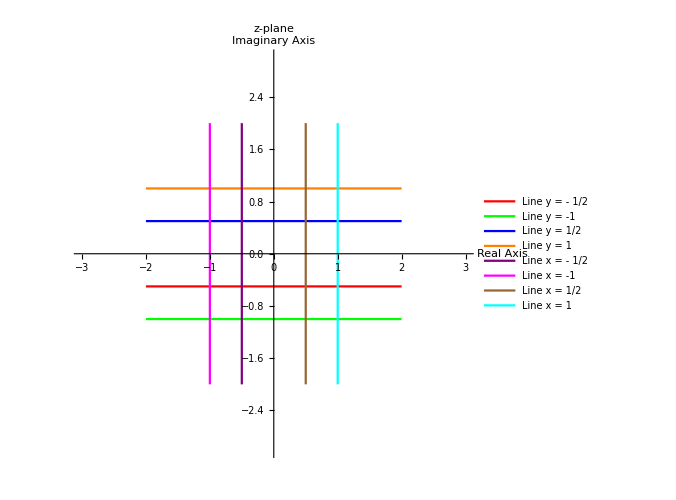
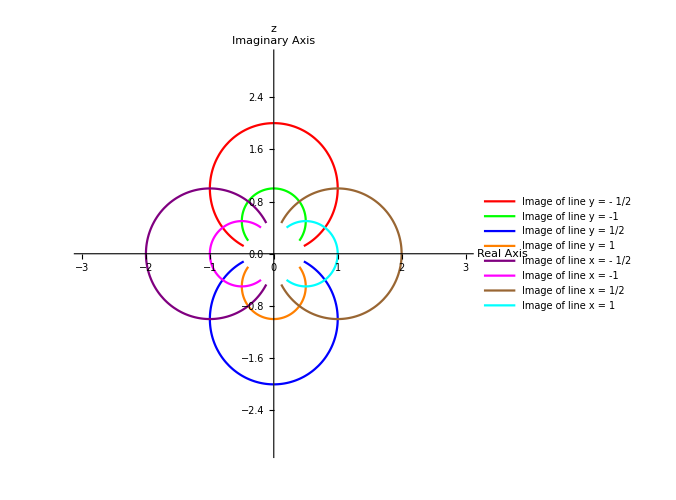

```mathematica
{Show[a1, a2], Show[b1, b2]}
```

Question 2: Plot the lines y = a, where a = 1/4 , 1/2 , 3/4 , 1; the lines x = a, where a = 1/4 , 1/2 , 3/4 , 1 and the corresponding grid. Also find the image of this grid under the mapping f(z) = z^2.

```mathematica
f[z_] := z^2
```

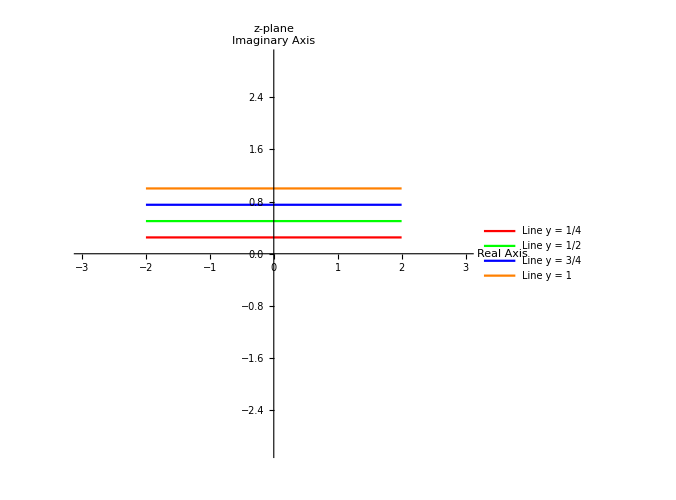

```mathematica
a1 = ParametricPlot[Evaluate[Table[{Re[t + ⅈ a], Im[t + ⅈ a]}, {a, {1/4, 1/2, 3/4, 1}}]], {t, -2, 2}, PlotStyle -> {Red, Green, Blue, Orange}, Axes -> True, Frame -> False, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotLabel -> "z-plane", PlotLegends -> {"Line y = 1/4 ", "Line y = 1/2", "Line y = 3/4 ", "Line y = 1"}, PlotRange -> 3, ImageSize -> {500, 500}]
```

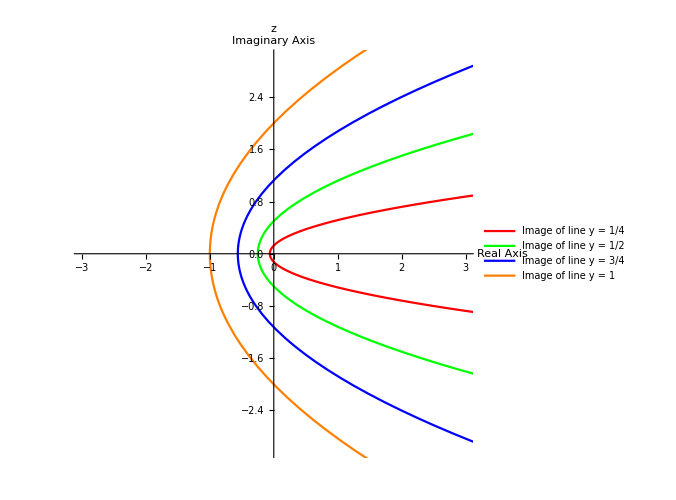

```mathematica
b1 = ParametricPlot[ Evaluate[Table[{Re[f[t + ⅈ a]], Im[f[t + ⅈ a]]}, {a, {1/4,1/2,3/4,1}}]], {t, -2, 2}, PlotStyle -> {Red, Green, Blue, Orange}, Axes -> True, Frame -> False, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotLabel -> "z", PlotLegends -> {"Image of line y = 1/4 ", "Image of line y = 1/2", "Image of line y = 3/4 ", "Image of line y = 1"}, PlotRange -> 3, ImageSize -> {500, 500}]
```

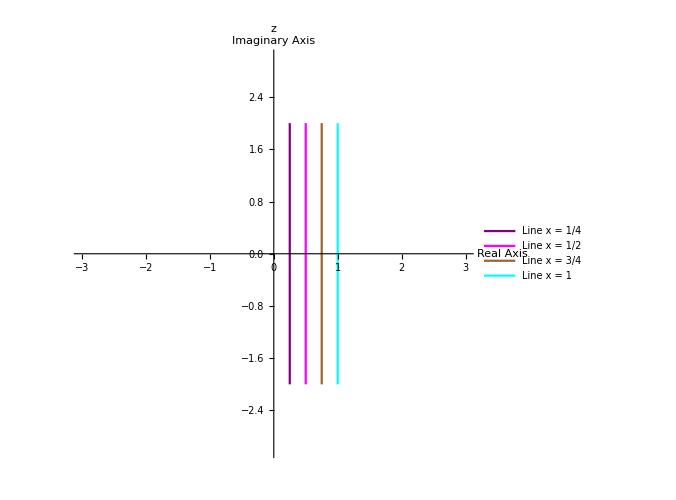

```mathematica
a2 = ParametricPlot[Evaluate[Table[{Re[a + ⅈ t], Im[a +ⅈ t]}, {a, {1/4,1/2,3/4,1}}]], {t, -2, 2}, PlotStyle -> {Purple, Magenta, Brown, Cyan}, Axes -> True, Frame -> False, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotLabel -> "z", PlotLegends -> {"Line x = 1/4 ", "Line x = 1/2", "Line x = 3/4 ", "Line x = 1"}, PlotRange -> 3, ImageSize -> {500, 500}]
```

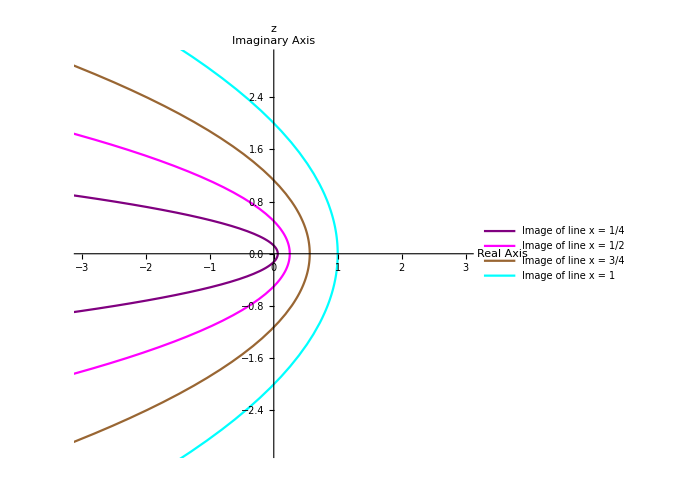

```mathematica
b2 = ParametricPlot[ Evaluate[Table[{Re[f[a + ⅈ t]], Im[f[a + ⅈ t]]}, {a, {1/4,1/2,3/4,1}}]], {t, -2, 2}, PlotStyle -> {Purple, Magenta, Brown, Cyan}, Axes -> True, Frame -> False, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotLabel -> "z", PlotLegends -> {"Image of line x = 1/4 ", "Image of line x = 1/2", "Image of line x = 3/4 ", "Image of line x = 1"}, PlotRange -> 3, ImageSize -> {500, 500}]
```

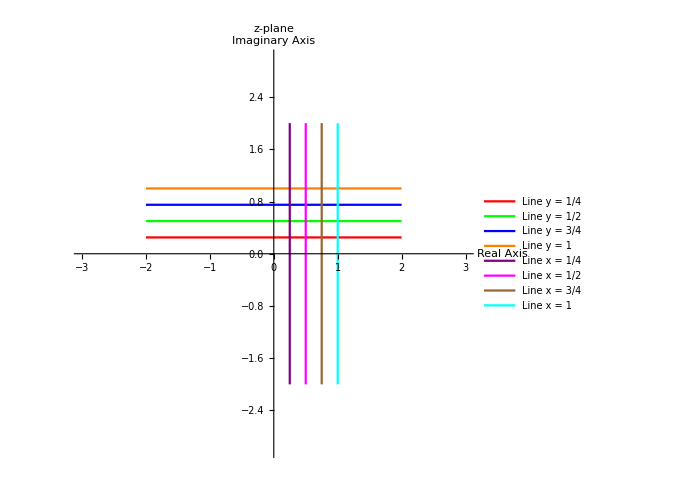
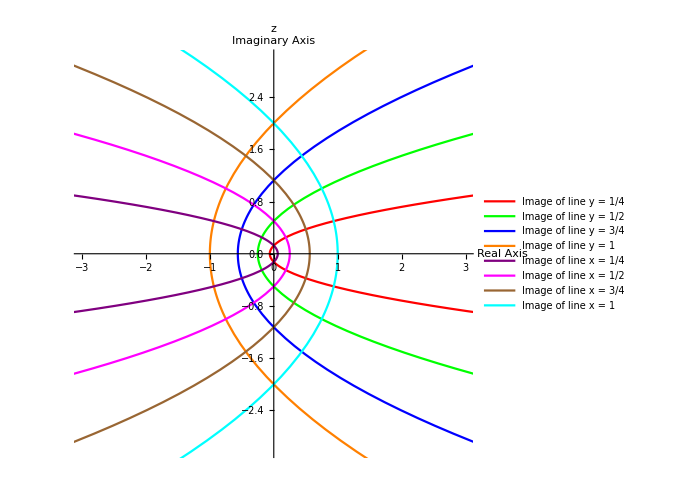

```mathematica
{Show[a1, a2], Show[b1, b2]}
```

NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 8 : Find a parametrization of a line segment joining the two specified end points. Also plot the line segment

1.1 : z0 = -1 + ⅈ , z1 = 2 - ⅈ

```mathematica
(* Initial and Terminal points *) 
z0 = -1 + ⅈ; z1 = 2 - ⅈ; 
(* Real and Imaginary parts of given points *) 
x0 = Re[z0]; 
y0 = Im[z0]; 
x1 = Re[z1]; 
y1 = Im[z1];
```

```mathematica
z[t_] = (x0 + (x1 - x0) t) + ⅈ (y0 + (y1 - y0) t);
```

```mathematica
dot0 = Graphics[{PointSize[0.03], Red, Point[{Re[z0], Im[z0]}]}]; 
dot1 = Graphics[{PointSize[0.03], Green, Point[{Re[z1], Im[z1]}]}];
```

```mathematica
line = ParametricPlot[{Re[z[t]], Im[z[t]]}, {t, 0, 1}, PlotRange -> {{-2, 3}, {-2, 2}}, 
Ticks -> {Range[-2, 3, 1 / 2], Range[-2, 2, 1 / 2]}, PlotStyle -> Blue, AxesLabel -> {"Real Axis", "Imaginary Axis"}];
```

Equation of the line segment joining the points -1+ⅈ and 2-ⅈ is

z[t] = -1+ⅈ (1-2 t)+3 t where 0 ≤ t ≤ 1

The required plot is

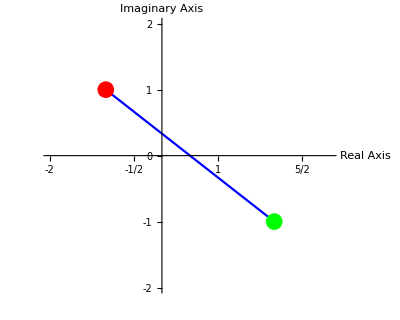

```mathematica
Print["Equation of the line segment joining the points ", z0, " and ", z1, " is "]; 
Print[" z[t] = ", z[t], " where 0 ≤ t ≤ 1"]; 
Print["The required plot is "]; 
Show[line, dot0, dot1]
```

1.2 : z0 = -1 + 3 ⅈ,  z1 = 2 + ⅈ

```mathematica
(* Initial and Terminal points *) 
z0 = -1 + 3 ⅈ; z1 = 2 + ⅈ; 
(* Real and Imaginary parts of given points *) 
x0 = Re[z0]; 
y0 = Im[z0]; 
x1 = Re[z1]; 
y1 = Im[z1];
```

```mathematica
z[t_] = (x0 + (x1 - x0) t) + ⅈ (y0 + (y1 - y0) t);
```

```mathematica
dot0 = Graphics[{PointSize[0.03], Red, Point[{Re[z0], Im[z0]}]}]; 
dot1 = Graphics[{PointSize[0.03], Green, Point[{Re[z1], Im[z1]}]}];
```

```mathematica
line = ParametricPlot[{Re[z[t]], Im[z[t]]}, {t, 0, 1}, PlotRange -> {{-2, 3}, {-2, 2}}, 
Ticks -> {Range[-2, 3, 1 / 2], Range[-2, 2, 1 / 2]}, PlotStyle -> Blue, AxesLabel -> {"Real Axis", "Imaginary Axis"}];
```

Equation of the line segment joining the points -1+3 ⅈ and 2+ⅈ is

z[t] = -1+ⅈ (3-2 t)+3 t where 0 ≤ t ≤ 1

The required plot is

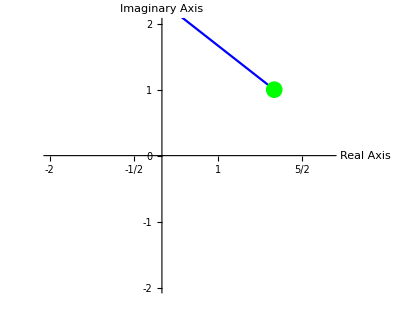

```mathematica
Print["Equation of the line segment joining the points ", z0, " and ", z1, " is "]; 
Print[" z[t] = ", z[t], " where 0 ≤ t ≤ 1"]; 
Print["The required plot is "]; 
Show[line, dot0, dot1]
```

1.3 : z0 = -2 - ⅈ , z1 = 1 + ⅈ

```mathematica
(* Initial and Terminal points *) 
z0 = -2 - ⅈ; z1 = 1 + ⅈ; 
(* Real and Imaginary parts of given points *) 
x0 = Re[z0]; 
y0 = Im[z0]; 
x1 = Re[z1]; 
y1 = Im[z1];
```

```mathematica
Clear[z]
z[t_] = (x0 + (x1 - x0) t) + ⅈ (y0 + (y1 - y0) t);
```

```mathematica
dot0 = Graphics[{PointSize[0.03], Red, Point[{Re[z0], Im[z0]}]}]; 
dot1 = Graphics[{PointSize[0.03], Green, Point[{Re[z1], Im[z1]}]}];
```

```mathematica
line = ParametricPlot[{Re[z[t]], Im[z[t]]}, {t, 0, 1}, PlotRange -> {{-2, 3}, {-2, 2}}, 
Ticks -> {Range[-2, 3, 1 / 2], Range[-2, 2, 1 / 2]}, PlotStyle -> Blue, AxesLabel -> {"Real Axis", "Imaginary Axis"}];
```

Equation of the line segment joining the points -2-ⅈ and 1+ⅈ is

z[t] = -2+3 t+ⅈ (-1+2 t) where 0 ≤ t ≤ 1

The required plot is

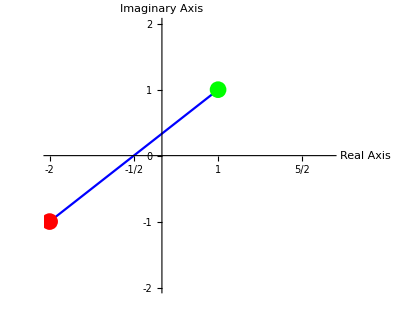

```mathematica
Print["Equation of the line segment joining the points ", z0, " and ", z1, " is "]; 
Print[" z[t] = ", z[t], " where 0 ≤ t ≤ 1"]; 
Print["The required plot is "]; 
Show[line, dot0, dot1]
```

Question 2: Find a parametrization of a polygonal path C. Also make a plot of it.

2.1 : C = C1 + C2 + C3 from - 1 + ⅈ to 3 - ⅈ 
	where  C1 is a line from - 1 + ⅈ to - 1, 
    		C2 is a line from - 1 to 1 + ⅈ, 
            		C3 is a line from 1 + ⅈ to 3 - ⅈ.

```mathematica
(* Initial and Terminal points of the paths Ci *) 
z0 = -1 + ⅈ; z1 = -1; z2 = 1 + ⅈ; z3 = 3 - ⅈ; 
(* Real and Imaginary parts of given points *) 
x0 = Re[z0]; 
y0 = Im[z0]; 
x1 = Re[z1]; 
y1 = Im[z1]; 
x2 = Re[z2]; 
y2 = Im[z2]; 
x3 = Re[z3];
y3 = Im[z3];
```

```mathematica
(* Equation of path C1: Line joining z0 to z1 *)
p1[t_] = (x0 + (x1 - x0) t) +ⅈ (y0 + (y1 - y0) t); 
(* Equation of path C2: Line joining z1 to z2 *) 
p2[t_] = (x1 + (x2 - x1) t) +ⅈ (y1 + (y2 - y1) t); 
(* Equation of path C3: Line joining z2 to z3 *) 
p3[t_] = (x2 + (x3 - x2) t) + ⅈ (y2 + (y3 - y2) t);
```

```mathematica
dot0 = Graphics[{PointSize[0.03], Red, Point[{Re[z0], Im[z0]}]}]; 
dot1 = Graphics[{PointSize[0.03], Green, Point[{Re[z1], Im[z1]}]}]; 
dot2 = Graphics[{PointSize[0.03], Blue, Point[{Re[z2], Im[z2]}]}]; 
dot3 = Graphics[{PointSize[0.03], Orange, Point[{Re[z3], Im[z3]}]}];
```

```mathematica
line = ParametricPlot[ {{Re[p1[t]], Im[p1[t]]}, 
{Re[p2[t]], Im[p2[t]]}, {Re[p3[t]], Im[p3[t]]}}, {t, 0, 1}, 
PlotRange -> {{-2, 4}, {-2, 2}}, PlotStyle -> {Purple},
AxesLabel -> {"Real Axis", "Imaginary Axis"}];
```

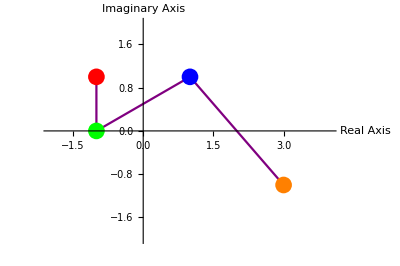

```mathematica
Show[line, dot0, dot1, dot2, dot3]
```

Question 3: Find a parametrization of the given curve. Also make a plot of it.

3.1 : C is the portion of the parabola x = y^2 + 2 y joining - 1 - ⅈ to 3 + ⅈ.

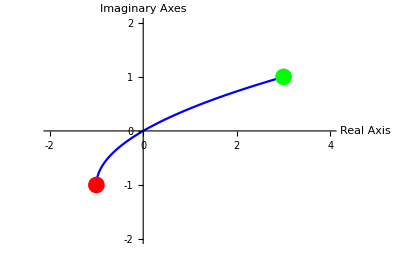

```mathematica
Clear[z]
z[t_] = (t^2 + 2 t) + ⅈ t; 
g1 = ParametricPlot[{Re[z[t]], Im[z[t]]}, {t, -1, 1}, 
PlotRange -> {{-2, 4}, {-2, 2}}, Ticks -> {Range[-2, 4, 1], 
Range[-2, 2, 1]}, AxesLabel -> {"Real Axis", "Imaginary Axes"},
PlotStyle -> Blue];

g2 = Graphics[{PointSize[0.03], Red, Point[{-1, -1}], Green, Point[{3, 1}]}]; 

Show[ g1, g2]
```

3.2 : C is the upper semicircle with radius 1 centered at point (2, 0) in the anticlockwise sense.

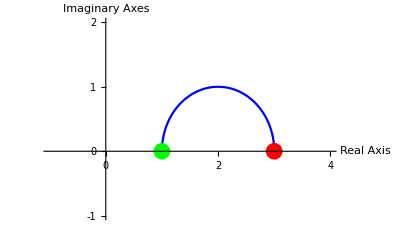

```mathematica
Clear[z]
z[t_] = (2 + Cos[t]) + ⅈ Sin[t]; 
g1 = ParametricPlot[{Re[z[t]], Im[z[t]]}, {t, 0, π}, 
PlotRange -> {{-1, 4}, {-1, 2}}, Ticks -> {Range[-2, 4, 1], Range[-2, 2, 1]}, 
AxesLabel -> {"Real Axis", "Imaginary Axes"}, PlotStyle -> Blue]; 
g2 = Graphics[{PointSize[0.03], Red, Point[{3, 0}], Green, Point[{1, 0}]}]; 
Show[ g1, g2]
```

NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 9 : Plot the line segment joining the two specified end points. And find the integral of the given function over that specified line segment.

1. f (z) = z, z0 = -1 + 3 ⅈ, z1 = 2 + ⅈ

```mathematica
Integrate[z, {z, -1 + 3 ⅈ, 2 + ⅈ}]
```

11/2+5 ⅈ

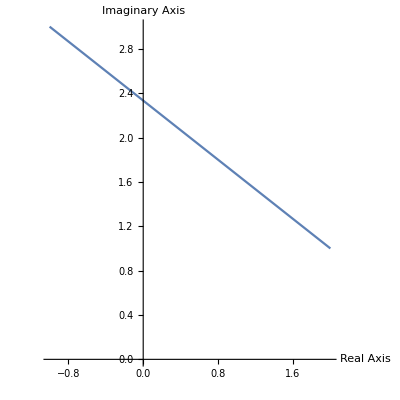

The value of the integration is

 C z ⅆz = 11/2+5 ⅈ

where C: c[t] = -1+ⅈ (3-2 t)+3 t, for 0 ≤ t ≤ 1.

```mathematica
ClearAll;
f[z_] = z ; 
z0 = -1 + 3 ⅈ; 
z1 = 2 + ⅈ; 
x0 = Re[z0]; y0 = Im[z0]; 
x1 = Re[z1]; y1 = Im[z1];
L[t_] = x0 + (x1 - x0) t + ⅈ (y0 + (y1 - y0) t); 
w[t_] = f[L[t]] * L'[t];
W1 = Integrate[w[t],{t, 0,1} ];

ParametricPlot[{Re[L[t]], Im[L[t]]}, {t, 0, 1}, Axes -> True, AxesOrigin -> {0, 0}, AxesLabel -> {"Real Axis", "Imaginary Axis"}] 

Print["The value of the integration is"]; 
Print[" C ", f[z], " ⅆz = ", W1]; 
Print["where C: c[t] = ", L[t], ", for 0 ≤ t ≤ 1."];
```

2.  f (z) = z, z0 = -1 - ⅈ, z1 = 3 + ⅈ

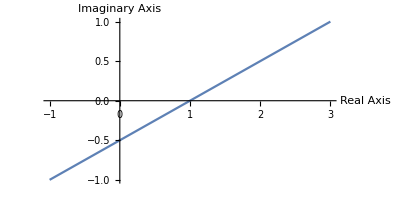

The value of the integration is

 C z ⅆz = 4+2 ⅈ

where C: c[t] = -1+4 t+ⅈ (-1+2 t), for 0 ≤ t ≤ 1.

```mathematica
f[z_] = z ; z0 = -1 - ⅈ; 
z1 = 3 + ⅈ; 

x0 = Re[z0]; y0 = Im[z0]; 
x1 = Re[z1]; y1 = Im[z1]; 

L[t_] = x0 + (x1 - x0) t + ⅈ (y0 + (y1 - y0) t); 
w[t_] = ComplexExpand[f[L[t]] * L'[t]];
W1 = Integrate[w[t], {t, 0, 1}] ; 

ParametricPlot[{Re[L[t]], Im[L[t]]}, {t, 0, 1}, Axes -> True, 
AxesOrigin -> {0, 0}, AxesLabel -> {"Real Axis", "Imaginary Axis"}]

Print["The value of the integration is"];
Print[" C ", f[z], " ⅆz = ", W1]; 
Print["where C: c[t] = ", L[t], ", for 0 ≤ t ≤ 1."];
```

3: f (z) = sin z, z0 = -1 + ⅈ, z1 = 2 - ⅈ

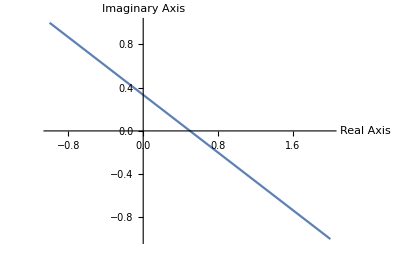

The value of the integration is

 C Sin[z] ⅆz = Cosh[1+ⅈ]-Cosh[1+2 ⅈ]

where C: c[t] = -1+ⅈ (1-2 t)+3 t, for 0 ≤ t ≤ 1.

```mathematica
f[z_] = Sin[z] ; 
z0 = -1 + ⅈ; 
z1 = 2- ⅈ; 

x0 = Re[z0]; y0 = Im[z0]; 
x1 = Re[z1]; y1 = Im[z1]; 

L[t_] = x0 + (x1 - x0) t + ⅈ (y0 + (y1 - y0) t); 
w[t_] = ComplexExpand[f[L[t]] * L'[t]];
W1 = Integrate[w[t], {t, 0, 1}] ; 

ParametricPlot[{Re[L[t]], Im[L[t]]}, {t, 0, 1}, Axes -> True, 
AxesOrigin -> {0, 0}, AxesLabel -> {"Real Axis", "Imaginary Axis"}]

Print["The value of the integration is"];
Print[" C ", f[z], " ⅆz = ", W1]; 
Print["where C: c[t] = ", L[t], ", for 0 ≤ t ≤ 1."];
```

4 : f (z) = z, z0 = -1 +ⅈ, z1 = 2 - ⅈ

```mathematica
f[z_] = Conjugate[z] ; 
z0 = -1 + ⅈ; 
z1 = 2- ⅈ; 

x0 = Re[z0]; y0 = Im[z0]; 
x1 = Re[z1]; y1 = Im[z1]; 

L[t_] = x0 + (x1 - x0) t + ⅈ (y0 + (y1 - y0) t); 
w[t_] = ComplexExpand[f[L[t]] * L'[t]];
W1 = Integrate[w[t], {t, 0, 1}] ; 

ParametricPlot[{Re[L[t]], Im[L[t]]}, {t, 0, 1}, Axes -> True, 
AxesOrigin -> {0, 0}, AxesLabel -> {"Real Axis", "Imaginary Axis"}]

Print["The value of the integration is"];
Print[" C ", f[z] //TraditionalForm, " ⅆz = ", W1]; 
Print["where C: c[t] = ", L[t], ", for 0 ≤ t ≤ 1."];
```

-Graphics-

The value of the integration is

 C Conjugate[z] ⅆz = 3/2-ⅈ

where C: c[t] = -1+ⅈ (1-2 t)+3 t, for 0 ≤ t ≤ 1.

NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 10 : Perform the following Line integrals.

1 : Perform the contour integration ∫_C 1/(z-2)ⅆz  
	where C is the upper semicircle with radius 1 centered at point (2, 0) in the anticlockwise sense

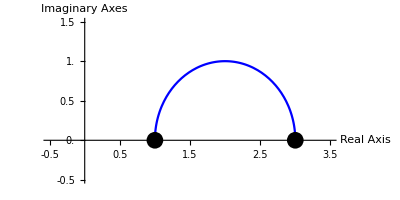

The Value of the contour integration ∫_C 1/(-2+z)ⅆz is ∫_0^π f[z[t]]z'[t]ⅆt = ⅈ π

where C: z[t] = 2+Cos[t]+ⅈ Sin[t], for 0 ≤ t ≤ π.

```mathematica
f[z_] = 1/(z - 2) ; 
z[t_] = (2 + Cos[t]) + ⅈ Sin[t]; 
val = Integrate [f[z[t]] * z '[t], {t, 0, π}]; 
V[t_] = ComplexExpand[{Re[z[t]], Im[z[t]]}]; 

g1 = ParametricPlot[V[t], {t, 0, π}, PlotRange -> {{-0.5, 3.5}, {-0.5, 1.5}},
Ticks -> {Range[-0.5, 3.5, 0.5], Range[-0.5, 1.5, 0.5]}, 
AxesLabel -> {"Real Axis", "Imaginary Axes"}, PlotStyle -> Blue]; 

g2 = Graphics[{PointSize[0.03], Point[{3, 0}], Point[{1, 0}]}]; 

Show[g1, g2] 
Print["The Value of the contour integration ", "∫_C ", f[z], "ⅆz is ", "∫_0^π ", "f[z[t]]z'[t]", "ⅆt ", "= ", val]; 
Print["where C: z[t] = ", z[t], ", for 0 ≤ t ≤ π."];
```

2 : Perform the contour integration ∫_C (2z)/(z^2+2)ⅆz
	where C is the circle z - ⅈ = 1 taken in anticlockwise sense.

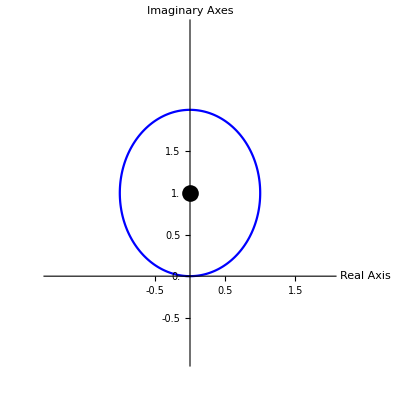

The Value of the contour integration ∫_C (2 z)/(2+z^2)ⅆz is ∫_0^(2  π) f[z[t]]z'[t]ⅆt = 2 ⅈ π

where C: z[t] = Cos[t]+ⅈ (1+Sin[t]), for 0 ≤ t ≤ π.

```mathematica
f[z_] = (2 z)/( z^2 + 2) ; 
z[t_] = Cos[t] + ⅈ (1 + Sin[t]); 
val = Integrate[ f[z[t]] * z '[t], {t, 0, 2 π}]; 
V[t_] = ComplexExpand[{Re[z[t]], Im[z[t]]}]; 

g1 = ParametricPlot[V[t], {t, 0, 2π}, PlotRange -> {{-2,2}, {-1, 3}},
Ticks -> {Range[-0.5, 3.5, 0.5], Range[-0.5, 1.5, 0.5]}, 
AxesLabel -> {"Real Axis", "Imaginary Axes"}, PlotStyle -> Blue]; 

g2 = Graphics[{PointSize[0.03], Point[{0, 1}]}]; 

Show[g1, g2] 
Print["The Value of the contour integration ", "∫_C ", f[z], "ⅆz is ", "∫_0^(2  π) ", "f[z[t]]z'[t]", "ⅆt ", "= ", val]; 
Print["where C: z[t] = ", z[t], ", for 0 ≤ t ≤ π."];
```

3 : Perform the contour integration ∫_C 1/z ⅆz
	where C is the circle z = 1 taken in clockwise sense.

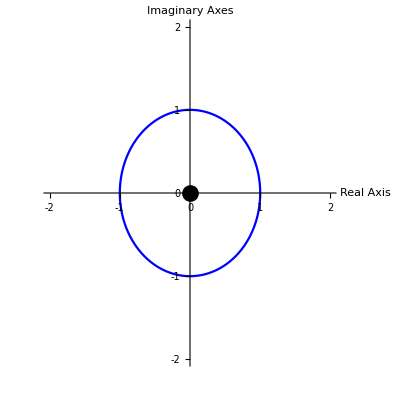

The Value of the contour integration ∫_C 1/z ⅆz is ∫_0^π  f[z[t]]z'[t]ⅆt = -2 ⅈ π

where C: z[t] = ⅈ Cos[t]+Sin[t], for 0 ≤ t ≤ π.

```mathematica
ClearAll;
f[z_] = 1/z ; 
z[t_] = Sin[t] + ⅈ Cos[t]; 
val = Integrate[ f[z[t]]*z'[t], {t, 0, 2 π}];
V[t_] = ComplexExpand[{Re[z[t]], Im[z[t]]}]; 

g1 = ParametricPlot[V[t], {t, 0, 2 π}, PlotRange -> {{-2,2}, {-2,2}},
Ticks -> {Range[-2,2,1], Range[-2,2,1]}, 
AxesLabel -> {"Real Axis", "Imaginary Axes"}, PlotStyle -> Blue]; 

g2 = Graphics[{PointSize[0.03], Point[{0, 0}]}]; 

Show[g1, g2] 
Print["The Value of the contour integration ", "∫_C ", f[z], "ⅆz is ", "∫_0^π  ", "f[z[t]]z'[t]", "ⅆt ", "= ", val]; 
Print["where C: z[t] = ", z[t], ", for 0 ≤ t ≤ π."];
```

4 : Perform the contour integration ∫_C z^3+2 z^2+1ⅆz
	where C is the contour given by x2 + y2 = 1 taken in the positive sense.

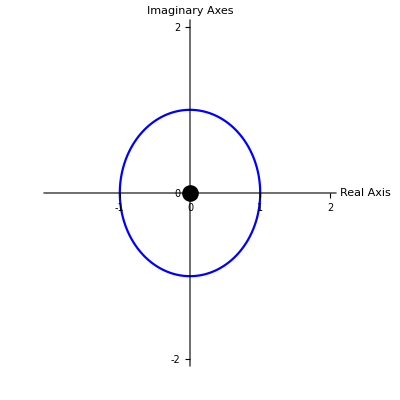

The Value of the contour integration ∫_C 1+2 z^2+z^3ⅆz is ∫_0^(2  π)  f[z[t]]z'[t]ⅆt = 0

where C: z[t] = Cos[t]+ⅈ Sin[t], for 0 ≤ t ≤ π.

```mathematica
f[z_] = z^3 + 2 z^2 + 1; 
z[t_] = Cos[t] + ⅈ Sin[t]; 
val = Integrate[f[z[t]] * z '[t], {t,0,2 π}];
V[t_] = ComplexExpand[{Re[z[t]], Im[z[t]]}]; 

g1 = ParametricPlot[V[t], {t, 0, 2 π}, PlotRange -> {{-2, 2}, {-2, 2}},
Ticks -> {Range[-1, 2, 1], Range[-2, 2, 2]}, 
AxesLabel -> {"Real Axis", "Imaginary Axes"}, PlotStyle -> Blue]; 

g2 = Graphics[{PointSize[0.03], Point[{0, 0}]}]; 

Show[g1, g2] 
Print["The Value of the contour integration ", "∫_C ", f[z], "ⅆz is ", "∫_0^(2  π)  ", "f[z[t]]z'[t]", "ⅆt ", "= ", val]; 
Print["where C: z[t] = ", z[t], ", for 0 ≤ t ≤ π."];
```

NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 11 : Perform the following Line integrals.

1 : Perform the contour integration  C z dz 
	where C is the portion of the parabola x = y2 + 2 y joining - 1 - ⅈ to 3 + ⅈ.

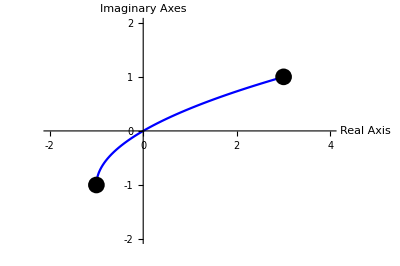

The Value of the contour integration  C zⅆz is  -1 1 f[z[t]]z'[t]ⅆt = 4+2 ⅈ

where C: z[t] = (2+ⅈ) t+t^2, for -1 ≤ t ≤ 1

```mathematica
ClearAll;
f[z_] = z; 
z[t_] = (t^2 + 2 t) + ⅈ t; 
val = Integrate[ f[z[t]] * z '[t], {t,-1,1}];
V[t_] = ComplexExpand[{Re[z[t]], Im[z[t]]}];

g1 = ParametricPlot[V[t], {t, -1, 1}, PlotRange -> {{-2, 4}, {-2, 2}}, 
Ticks -> {Range[-2, 4, 1], Range[-2, 2, 1]}, 
AxesLabel -> {"Real Axis", "Imaginary Axes"}, PlotStyle -> Blue];

g2 = Graphics[{PointSize[0.03], Point[{-1, -1}], Point[{3, 1}]}]; 
Show[g1, g2] 
Print["The Value of the contour integration ", " C ", f[z], "ⅆz is ", " -1 1 ", "f[z[t]]z'[t]", "ⅆt ", "= ", val]; 
Print["where C: z[t] = ", z[t], ", for -1 ≤ t ≤ 1"];
```

2 : Perform the contour integration  C z2 - 2 z + 1 dz 
	where C is the contour given by x = y2 + 1 where - 2 ≤ y ≤ 2.

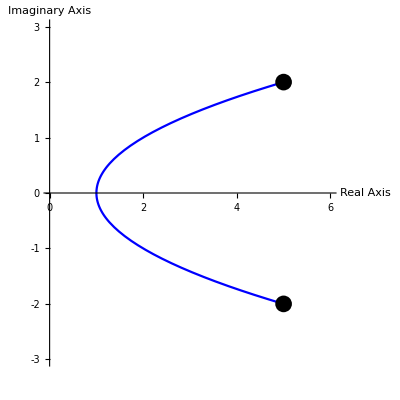

The Value of the contour integration  C 1+2 z+z^2 ⅆz is  -2 2 f[z[t]]z'[t]ⅆt = (416 ⅈ)/3

where C: z[t] = 1+ⅈ t+t^2, for -2 ≤ t ≤ 2

```mathematica
f[z_] = z^2 + 2* z + 1; 
z[t_] = (t^2 + 1) + ⅈ t; 
val = Integrate[ f[z[t]] * z'[t],{t,-2,2}];
V[t_] = ComplexExpand[{Re[z[t]], Im[z[t]]}]; 

g1 = ParametricPlot[V[t], {t, -2, 2}, PlotRange -> {{0, 6}, {-3, 3}}, 
Ticks -> {Range[0, 6, 1], Range[-3, 3, 1]}, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotStyle -> Blue];

g2 = Graphics[{PointSize[0.03], Point[{5, -2}], Point[{5, 2}]}]; Show[g1, g2]

Print["The Value of the contour integration ", " C ", f[z], " ⅆz is ", " -2 2 ", "f[z[t]]z'[t]", "ⅆt ", "= ", val]; 
Print["where C: z[t] = ", z[t], ", for -2 ≤ t ≤ 2"];
```

3 : Show that  C1 z dz =  C2 z dz 
	where C1 is the line segment from - 1 - ⅈ to 3 + ⅈ and 
    		C2 is the portion of the parabola x = y2 + 2 y joining - 1 - ⅈ to 3 + ⅈ . 
   Also plot the contours C1 and C2 .

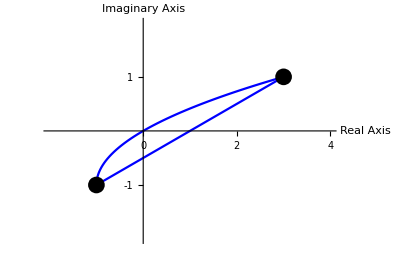

```mathematica
ClearAll;
f[z_] = z; 
z0 = -1 - ⅈ; 
z1 = 3 + ⅈ; 
x0 = Re[z0]; y0 = Im[z0]; 
x1 = Re[z1]; y1 = Im[z1]; 
c1[t_] = x0 + (x1 - x0) t + ⅈ(y0 + (y1 - y0) t); 
c2[t_] = (t^2 + 2 t) + ⅈ t; 

Int1 = Integrate[f[c1[t]] *(c1'[t]), {t,0,1}]; 
Int2 = Integrate[f[c2[t]] * (c2'[t]), {t, -1,1}];

V1[t_] = ComplexExpand[{Re[c1[t]], Im[c1[t]]}];
V2[t_] = ComplexExpand[{Re[c2[t]], Im[c2[t]]}]; 

g1 = ParametricPlot[V1[t], {t, 0, 1}, PlotRange -> {{-2, 4}, {-2, 2}}, Ticks -> {Range[0, 6, 1], Range[-3, 3, 1]}, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotStyle -> Blue]; g2 = ParametricPlot[V2[t], {t, -1, 1}, PlotRange -> {{-2, 4}, {-2, 2}}, Ticks -> {Range[0, 6, 1], Range[-3, 3, 1]}, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotStyle -> Blue];
g3 = Graphics[{PointSize[0.03], Point[{x0, y0}], Point[{x1, y1}]}]; 
Show[g1, g2, g3]
```

```mathematica
If[Int1== Int2, 
Print["The integrals  C1 z dz and  C2 z dz are equal and equal to ", Int1, "." ],Print["Integrals are not equal."]]
```

The integrals  C1 z dz and  C2 z dz are equal and equal to 4+2 ⅈ.

NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 12 : Use ML-inequality to show that |∫_C 1/(z^2+1)ⅆz|<= 1/5 ,where C is the line segment form 2 to 2 + ⅈ. While solving, represent the distance from the point z to the points ⅈ and -ⅈ, respectively

1/5

1

An upper bound to the absolute value of the integral |∫_C 1/z^2ⅆz| is found to be 1/5.

{2,0.465359}

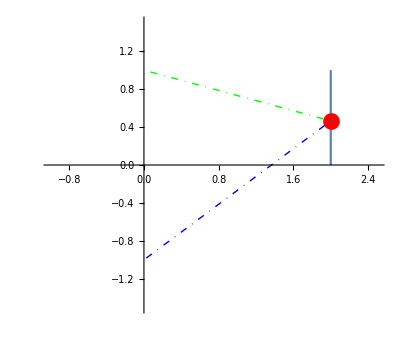

```mathematica
f[z_]:=1/(z^2+1)
c[t_]:=2+ⅈ t
k[t_]:=ComplexExpand[f[c[t]]]
r[t_]:=Refine[Re[k[t]],t ∈ Reals]
s[t_]:=Refine[Im[k[t]],t ∈ Reals]
A[t_]:=Simplify[√(s[t]^2+r[t]^2)]
M=MaxValue[{A[t],0<=t<=1},t]
L=∫_0^1 Abs[c'[t]]ⅆt
Print["An upper bound to the absolute value of the integral |∫_C 1/z^2ⅆz| is found to be ",M*L,"."]
p={2,RandomReal[{0,1}]}
a=ParametricPlot[{Re[c[t]],Im[c[t]]},{t,0,1},PlotRange->{{-1,2.5},{-1.5,1.5}}];
b=Graphics[{Red,PointSize[0.03],Point[p],Green,DotDashed,Line[{p,{0,1}}],Blue,DotDashed,Line[{p,{0,-1}}]}];
Show[a,b]
```

NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 13 : Series Representation

Let  be complex numbers for n ∈ Integers. The doubly infinite series   defined by
                                                                     
is called a Laurent Series about the point z = α.

7.1 Find the series representation for 
f (z) = (cos (z) - 1) / z^4 
that involves powers of z about z = 0.
Also plot the magnitude of the function and magnitude of its series expansion.

```mathematica
Normal[Series[f[z], {z, 0, 10}]]
```

f[0]+z f'[0]+1/2 z^2 f''[0]+1/6 z^3 f^(3)[0]+1/24 z^4 f^(4)[0]+1/120 z^5 f^(5)[0]+1/720 z^6 f^(6)[0]+(z^7 f^(7)[0])/5040+(z^8 f^(8)[0])/40320+(z^9 f^(9)[0])/362880+(z^10 f^(10)[0])/3628800

```mathematica
(* Laurent Series Expansion *) 
f[z_] = (Cos[z] - 1)/ z^4 ;
L[z_] = Normal[Series[f[z], {z, 0, 10}]] ; 
Print["The Laurent Series expansion for the function f(z) = ", f[z], ", is given by ", L[z], " + ... ."];
```

The Laurent Series expansion for the function f(z) = (-1+Cos[z])/z^4, is given by 1/24-1/(2 z^2)-z^2/720+z^4/40320-z^6/3628800+z^8/479001600-z^10/87178291200 + ... .

```mathematica
(*Magnitude of the function*) 
Plot3D[Abs[f[x + ⅈ y]], {x, -10, 10}, {y, -10, 10}]
```

-Graphics3D-

```mathematica
(*Magnitude of the Laurent Series*) 
Plot3D[Abs[L[x + ⅈ y]], {x, -10, 10}, {y, -10, 10}]
```

-Graphics3D-

7.2 : Find the Laurent series representation for 
f(z) = (sin (z) - 1)/ z^4 
that involves powers of z about z = 0. 
Also plot the magnitude of the function and magnitude of its Taylor series expansion.

```mathematica
(* Laurent Series Expansion *) 
f[z_] = (Sin[z] - 1) / z^4 ; 
L[z_] = Normal[Series[f[z], {z, 0, 10}]]; 
Print["The Laurent Series expansion for the function f(z) = ", f[z], ", is given by ", L[z], " + ... ."];
```

The Laurent Series expansion for the function f(z) = (-1+Sin[z])/z^4, is given by -1/z^4+1/z^3-1/(6 z)+z/120-z^3/5040+z^5/362880-z^7/39916800+z^9/6227020800 + ... .

```mathematica
(*Magnitude of the function*) 
Plot3D[Abs[f[x + ⅈ y]], {x, -10, 10}, {y, -10, 10}]
```

-Graphics3D-

```mathematica
(*Magnitude of the Laurent Series*) 
Plot3D[Abs[L[x + ⅈ y]], {x, -10, 10}, {y, -10, 10}]
```

-Graphics3D-

7.3 : Find the Laurent series representation for 
f(z) = (Cos(z))/ z^4 
that involves powers of z about z = 0. 
Also plot the magnitude of the function and magnitude of its Taylor series expansion.

```mathematica
(* Laurent Series Expansion *) 
f[z_] = (Cos[z]) / z^4 ; 
L[z_] = Normal[Series[f[z], {z, 0, 10}]]; 
Print["The Laurent Series expansion for the function f(z) = ", f[z], ", is given by ", L[z], " + ... ."];
```

The Laurent Series expansion for the function f(z) = Cos[z]/z^4, is given by 1/24+1/z^4-1/(2 z^2)-z^2/720+z^4/40320-z^6/3628800+z^8/479001600-z^10/87178291200 + ... .

```mathematica
(*Magnitude of the function*) 
Plot3D[Abs[f[x + ⅈ y]], {x, -10, 10}, {y, -10, 10}]
```

-Graphics3D-

```mathematica
(*Magnitude of the Laurent Series*) 
Plot3D[Abs[L[x + ⅈ y]], {x, -10, 10}, {y, -10, 10}]
```

-Graphics3D-

7.4: Find the Laurent series representation for 
f(z) = 1 / (2 + z + z^3)
that involves powers of z about z = 0. 
Also plot the magnitude of the function and magnitude of its Taylor series expansion.

```mathematica
(* Laurent Series Expansion *) 
f[z_] =1 / (2 + z + z^3) ; 
L[z_] = Normal[Series[f[z], {z, 0, 10}]]; 
Print["The Laurent Series expansion for the function f(z) = ", f[z], ", is given by ", L[z], " + ... ."];
```

The Laurent Series expansion for the function f(z) = 1/(2+z+z^3), is given by 1/2-z/4+z^2/8-(5 z^3)/16+(9 z^4)/32-(13 z^5)/64+(33 z^6)/128-(69 z^7)/256+(121 z^8)/512-(253 z^9)/1024+(529 z^10)/2048 + ... .

```mathematica
(*Magnitude of the function*) 
Plot3D[Abs[f[x + ⅈ y]], {x, -10, 10}, {y, -10, 10}]
```

-Graphics3D-

```mathematica
(*Magnitude of the Laurent Series*) 
Plot3D[Abs[L[x + ⅈ y]], {x, -10, 10}, {y, -10, 10}]
```

-Graphics3D-

7.5: Find the Laurent series representation for 
f(z) = ⅇ ^ (-1/z^2)
that involves powers of z about z = 0. 
Also plot the magnitude of the function and magnitude of its Taylor series expansion.

```mathematica
(* Laurent Series Expansion *) 
f[z_] =ⅇ^(z) ; 
T[z_] = Normal[Series[f[z], {z, 0, 10}]]
L[z_] = T[ -1/ z^2 ];
Print["The Laurent Series expansion for the function f(z) = ", f[-1/z^2], ", is given by ", L[z], " + ... ."];
```

1+z+z^2/2+z^3/6+z^4/24+z^5/120+z^6/720+z^7/5040+z^8/40320+z^9/362880+z^10/3628800

The Laurent Series expansion for the function f(z) = ⅇ^(-1/z^2), is given by 1+1/(3628800 z^20)-1/(362880 z^18)+1/(40320 z^16)-1/(5040 z^14)+1/(720 z^12)-1/(120 z^10)+1/(24 z^8)-1/(6 z^6)+1/(2 z^4)-1/z^2 + ... .

```mathematica
(*Magnitude of the function*) 
Plot3D[Abs[f[-1/(x + ⅈ y)^2]], {x, -10, 10}, {y, -10, 10}]
```

-Graphics3D-

```mathematica
(*Magnitude of the Laurent Series*) 
Plot3D[Abs[L[(x + ⅈ y)]], {x, -10, 10}, {y, -10, 10}]
```

-Graphics3D-

7.6: Find the Laurent series representation for 
f(z) = 3 / (2 + z - z^3)
that involves powers of z about z = 0. 
Also plot the magnitude of the function and magnitude of its Taylor series expansion.

```mathematica
Solve[2 + z - z^2 == 0, z]
```

{{z→-1},{z→2}}

```mathematica
(*About the point z = 0*)
(* Laurent Series Expansion *) 
f[z_] =3 / (2 + z - z^3) ; 
L1[z_] = Normal[Series[f[z], {z, 0, 10}]]; 
Print["The Laurent Series expansion for the function f(z) = ", f[z], ", is given by ", L1[z], " + ... ."];
```

The Laurent Series expansion for the function f(z) = 3/(2+z-z^3), is given by 3/2-(3 z)/4+(3 z^2)/8+(9 z^3)/16-(21 z^4)/32+(33 z^5)/64+(3 z^6)/128-(87 z^7)/256+(219 z^8)/512-(207 z^9)/1024-(141 z^10)/2048 + ... .

```mathematica
(*Magnitude of the function*) 
Plot3D[Abs[f[x + ⅈ y]], {x, -10, 10}, {y, -10, 10}]
```

-Graphics3D-

```mathematica
(*Magnitude of the Laurent Series*) 
Plot3D[Abs[L1[x + ⅈ y]], {x, -10, 10}, {y, -10, 10}]
```

-Graphics3D-

```mathematica
(* About the point z = -1 *)
(* Laurent Series Expansion *) 
f[z_] =3 / (2 + z - z^3) ; 
L2[z_] = Normal[Series[f[z], {z, -1, 10}]]; 
Print["The Laurent Series expansion for the function f(z) = ", f[z], ", is given by ", L2[z], " + ... ."];
```

The Laurent Series expansion for the function f(z) = 3/(2+z-z^3), is given by 3/2+(3 (1+z))/2-3/4 (1+z)^2-9/4 (1+z)^3-3/8 (1+z)^4+21/8 (1+z)^5+33/16 (1+z)^6-33/16 (1+z)^7-123/32 (1+z)^8+9/32 (1+z)^9+321/64 (1+z)^10 + ... .

```mathematica
(*Magnitude of the function*) 
Plot3D[Abs[f[x + ⅈ y]], {x, -10, 10}, {y, -10, 10}]
```

-Graphics3D-

```mathematica
(*Magnitude of the Laurent Series*) 
Plot3D[Abs[L2[x + ⅈ y]], {x, -10, 10}, {y, -10, 10}]
```

-Graphics3D-

NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 14 : Locate the poles of f(z) = 1/(z^4+26 z^2+5) and specify their order.

```mathematica
f[z_]:=1/(5 z^4+26 z^2+5);
Solve[1/f[z]==0,z]
```

{{z→-ⅈ/(√5)},{z→ⅈ/(√5)},{z→-ⅈ √5},{z→ⅈ √5}}

```mathematica
Text["The function f has poles at z=-i/(√5),z=i/(√5),z=-i√5 and at z=i√5 of order 1."]
```

The function f has poles at z=-i/(√5),z=i/(√5),z=-i√5 and at z=i√5 of order 1.

NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 15 : Locate the zero and poles of g(z) = (π cot(πt))/z^2 and determine their order. Also justify that Res(g,0)= -π^2/3.

```mathematica
f[z_]:=(Pi Cot[Pi z])/z^2;
Solve[Cot[Pi z]==0,z]
```

{{z→ConditionalExpression[(π/2+π C[1])/π, C[1]∈ℤ]}}

```mathematica
Text["Conclusion: The function f has zero at z=(π/2)/π(n ∈ Z) for order 1."]
Solve[1/f[z]==0,z]
```

Conclusion: The function f has zero at z=(π/2)/π(n ∈ Z) for order 1.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z→0}}

```mathematica
Text["Conclusion: The function f1 has pole at z=0 for order 2."]
```

Conclusion: The function f1 has pole at z=0 for order 2.

```mathematica
Residue[f[z],{z,0}]
```

-π^2/3

```mathematica
SeriesCoefficient[f[z],{z,0,-1}]
```

-π^2/3

NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 16 : A particular Contour Integral.

Ques: Perform the following Line Integrals.

(i) ∫_C exp(2/z)ⅆz
(ii) ∫_C 1/(z^4+z^3-2 z^2)ⅆz
where C is the unit circle with center at z = 0 taken in the positive sense.

The curve C can be parametrized as
C : z (t) = x (t) + ⅈ y(t) , 0 ⩽ t ⩽ 2 π
where x(t) = Cos[t] and y(t) = Sin[t]

```mathematica
c[t_]:=Cos[t]+ⅈ Sin[t];
```

(i) ∫_C exp(2/z)ⅆz

```mathematica
f[z_]:= e^(2/z)
val=∫_0^(2π) f[c[t]]*c'[t]ⅆt;
Print["The Value of the contour integration","∫_C ",f[z],"ⅆz is","= ",val];
Print["where C: z[t]=",c[t],", for 0 ≤ t ≤ 2π"];
```

The Value of the contour integration∫_C e^(2/z)ⅆz is= ConditionalExpression[0, Log[e]==0]

where C: z[t]=Cos[t]+ⅈ Sin[t], for 0 ≤ t ≤ 2π

(ii) ∫_C 1/(z^4+z^3-2 z^2)ⅆz

```mathematica
g[z_]:=1/(z^4+z^3-2 z^2)
Solve[1/g[z]==0,z]
```

{{z→-2},{z→0},{z→0},{z→1}}

```mathematica
Text["The function g has poles at z = 0 of order 2 and a pole at z = 1 of order 1."]
```

The function g has poles at z = 0 of order 2 and a pole at z = 1 of order 1.

```mathematica
Apart[g[z]]
```

1/(3 (-1+z))-1/(2 z^2)-1/(4 z)-1/(12 (2+z))

1/(z^4+z^3-2 z^2)=-1/(2 z^2)-1/(4 z)-1/(12 (2+z))+1/(3 (-1+z))
So that
∫_C 1/(z^4+z^3-2 z^2)=-∫_C 1/(2 z^2)-∫_C 1/(4 z)-∫_C 1/(12 (2+z))+∫_C 1/(3 (-1+z))
Using
(i) Cauchy's Integral formula :∫_C h[z]/(z-a)dz=2π ⅈ h[a]
(ii)Derivative of an analytic function: ∫_C h[z]/(z-a)^2 dz=2π ⅈ h'[a]
where a is any point inside or on C.

```mathematica
Subscript[h, 1][z_]:=1/2
Subscript[f, 1][z_]:=(Subscript[h, 1][z])/z^2
Subscript[h, 2][z_]:=1/4
Subscript[f, 2][z_]:=(Subscript[h, 2][z])/z
Subscript[h, 3][z_]:=1/12
Subscript[f, 3][z_]:=(Subscript[h, 3][z])/(z+2)
Subscript[h, 4][z_]:=1/3
Subscript[f, 4][z_]:=(Subscript[h, 4][z])/(z-1)
Subscript[Val, 1]=2π ⅈ(Subscript[h, 1]'[z]/.z->0);
Subscript[Val, 2]=2π ⅈ(Subscript[h, 2][z]/.z->0);
Subscript[Val, 3]=0;
(*function is analytic inside and on C*)
Subscript[Val, 4]=2π ⅈ(Subscript[h, 4][z]/.z->1);
V=-Subscript[Val, 1]-Subscript[Val, 2]-Subscript[Val, 3]+Subscript[Val, 4];
Print["The Value of the contour integration","∫_C ",f[z],"ⅆz is","= ",val];
Print["where C: z[t]=",c[t],", for 0 ≤ t ≤ 2π"];
```

The Value of the contour integration∫_C e^(2/z)ⅆz is= ConditionalExpression[0, Log[e]==0]

where C: z[t]=Cos[t]+ⅈ Sin[t], for 0 ≤ t ≤ 2π

(ii) ∫_C 1/(z^4+z^3-2 z^2)ⅆz

Using Method of Residues

```mathematica
g[z_]:=1/(z^4+z^3-2 z^2)
Solve[1/g[z]==0,z]
```

{{z→-2},{z→0},{z→0},{z→1}}

```mathematica
a=Residue[g[z],{z,0}]
```

-1/4

```mathematica
b=Residue[g[z],{z,1}]
```

1/3

```mathematica
Va1=2ⅈ π(a+b)
```

(ⅈ π)/6